```mathematica
getWeights[input_]:= If[input[[1]] == 1, {0.8, 0.2}, {0.5, 0.5}]
```

```mathematica
getCES2[nReps_, nSwitches_]:=Module[{causes, effects, ces},
causes = Table[Tuples[{0, 1}, nSwitches], nReps];
ces = Map[{#, RandomChoice[getWeights[#]-> {1, 0}]}&, causes, {2}]
]
```

```mathematica
showCES2[ces_]:= 
Grid[
Apply[{
ArrayPlot[{#1}, ImageSize->20],
"->",
GrayLevel[BitXor[#2]]}&,
ces, {2}
]]
```

```mathematica
getCounts[ces_]:=Map[Count[ces, #, 2 ]&,cases]
```

```mathematica
labels = {GrayLevel[1]->GrayLevel[0],GrayLevel[0]->GrayLevel[0],GrayLevel[1]->GrayLevel[1],GrayLevel[0]->GrayLevel[1]}
```

```mathematica
ces = getCES2[7, 3];
showCES2[ces]
```

{-Graphics-,->,GrayLevel[1]} | {-Graphics-,->,GrayLevel[0]} | {-Graphics-,->,GrayLevel[1]} | {-Graphics-,->,GrayLevel[0]} | {-Graphics-,->,GrayLevel[1]} | {-Graphics-,->,GrayLevel[1]} | {-Graphics-,->,GrayLevel[1]} | {-Graphics-,->,GrayLevel[0]}
{-Graphics-,->,GrayLevel[1]} | {-Graphics-,->,GrayLevel[1]} | {-Graphics-,->,GrayLevel[0]} | {-Graphics-,->,GrayLevel[0]} | {-Graphics-,->,GrayLevel[1]} | {-Graphics-,->,GrayLevel[1]} | {-Graphics-,->,GrayLevel[0]} | {-Graphics-,->,GrayLevel[1]}
{-Graphics-,->,GrayLevel[1]} | {-Graphics-,->,GrayLevel[0]} | {-Graphics-,->,GrayLevel[0]} | {-Graphics-,->,GrayLevel[0]} | {-Graphics-,->,GrayLevel[1]} | {-Graphics-,->,GrayLevel[1]} | {-Graphics-,->,GrayLevel[1]} | {-Graphics-,->,GrayLevel[0]}
{-Graphics-,->,GrayLevel[0]} | {-Graphics-,->,GrayLevel[1]} | {-Graphics-,->,GrayLevel[0]} | {-Graphics-,->,GrayLevel[0]} | {-Graphics-,->,GrayLevel[1]} | {-Graphics-,->,GrayLevel[1]} | {-Graphics-,->,GrayLevel[1]} | {-Graphics-,->,GrayLevel[1]}
{-Graphics-,->,GrayLevel[0]} | {-Graphics-,->,GrayLevel[1]} | {-Graphics-,->,GrayLevel[0]} | {-Graphics-,->,GrayLevel[1]} | {-Graphics-,->,GrayLevel[0]} | {-Graphics-,->,GrayLevel[1]} | {-Graphics-,->,GrayLevel[1]} | {-Graphics-,->,GrayLevel[1]}
{-Graphics-,->,GrayLevel[1]} | {-Graphics-,->,GrayLevel[1]} | {-Graphics-,->,GrayLevel[1]} | {-Graphics-,->,GrayLevel[1]} | {-Graphics-,->,GrayLevel[1]} | {-Graphics-,->,GrayLevel[0]} | {-Graphics-,->,GrayLevel[0]} | {-Graphics-,->,GrayLevel[1]}
{-Graphics-,->,GrayLevel[1]} | {-Graphics-,->,GrayLevel[1]} | {-Graphics-,->,GrayLevel[1]} | {-Graphics-,->,GrayLevel[0]} | {-Graphics-,->,GrayLevel[1]} | {-Graphics-,->,GrayLevel[1]} | {-Graphics-,->,GrayLevel[0]} | {-Graphics-,->,GrayLevel[0]}

```mathematica
labelsNum = Tuples[{0, 1}, 4];
cases =Join[Map[{#, 1}&, labelsNum], Map[{#, 0}&, labelsNum]];
bars =Thread[Table[getCounts[ces], 1]]
lbars = MapThread[Labeled[#1, #2]&,{bars, labels}];
BarChart[lbars]
```

```mathematica
Manipulate[ArrayPlot[Transpose[Tuples[{0, 1}, nSwitches]], Mesh-> True, ImageSize->{200*nSwitches, 100}], {nSwitches, 1, 10, 1}]
```

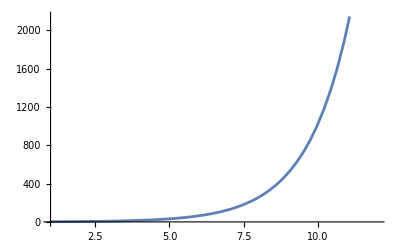

```mathematica
Plot[2^x, {x, 1, 12}]
```

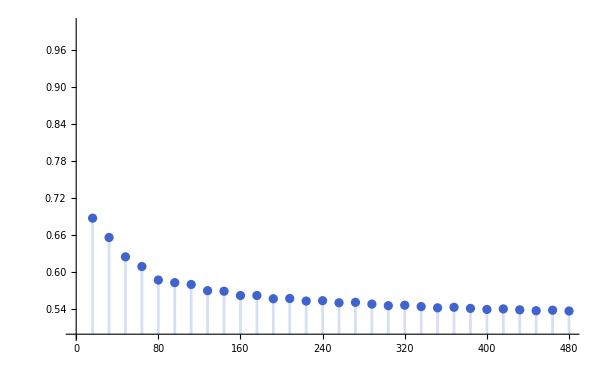
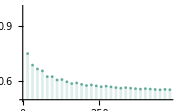
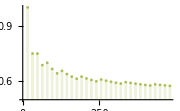
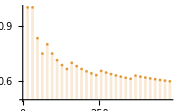
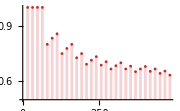

```mathematica
sMax = 5;
Row[Table[
DiscretePlot[Minimize[{c, 
  CDF[BinomialDistribution[n/(2^(s-1)), 10/20], c] >= 95/100 && 
   0 < c <= Floor[600/2^(s-1)]}, c, Integers][[1]]/(n/(2^(s-1))), {n, 2^(sMax-1), 30*2^(sMax-1), 2^(sMax-1)}, PlotRange->{{0, 30*2^(sMax-1)}, {0.5, 1}}, PlotStyle->ColorData["Rainbow"][s/sMax], ImageSize->Small], {s, sMax}]]
```